## Load library

```mathematica
SetDirectory[NotebookDirectory[]];
<< "TwoLink`"
DefaultPhysicalParameters[];
CompileFunctions[];
```

## Brachiation and Walking Functions

```mathematica
beqn[q_] := Evaluate[
Block[{var, t, f, x0, x , ξ, dξ, eqns, evnts},
var[1] = Array[(Subscript[x,#][t])&, 4];
f[1] = TwoLink`Dynamics`F[var[1], 0];
x0 = Thread[var[1]== {q, π-2q, 0, 0}] /. t-> 0;
eqns = Thread[D[var[1], t]== f[1]];

evnts = Method->{"EventLocator","Event"->  var[1]⟦1⟧,"EventAction":>Throw[{FixAngles[Subscript[x, 2][t]], 2 t}, "x1 = 0"],"EventLocationMethod"->"Brent"};

{{eqns, x0}, {}, {t, 50}, evnts, StartingStepSize->0.25, AccuracyGoal-> 12, PrecisionGoal-> 12, MaxSteps-> Infinity}
]
];

broot[{ql_, qu_}] := Module[{r, q},
r[q_?NumberQ] := First@Catch[NDSolve @@ beqn[q], "x1 = 0"];
q /. FindRoot[r[q], {q, ql, qu}]
];

bc[{ql_, qu_}] := Module[{q, t},
q = broot[{ql, qu}];
t = Last@Catch[NDSolve @@ beqn[q], "x1 = 0"];
{q, π-2q, 0, 0, t}
]
```

```mathematica
weqn[t_, up_:True] := Module[{A, DH, xeq},
xeq = {If[up, π, 0], π, 0, 0};
A = TwoLink`Dynamics`A[xeq, 0];
DH = TwoLink`Dynamics`DH[xeq];
(* ignore nearly singular warning messages *)
(* in general, using Quiet like this is not recommended *)
Quiet@Det[DH.MatrixExp[A t] - IdentityMatrix[Length@xeq]]
];

wroot[{tl_, tu_}, up_:True] := Module[{r, t},
r[t_?NumberQ] := weqn[t, up];
t /. FindRoot[r[t], {t, tl, tu}]
];

wc[{tl_, tu_}, up_:True] := Module[{q, t},
q = If[up, π, 0];
t = wroot[{tl, tu}, up];
{q, π, 0, 0, t}
];
```

## Find the seed values

The  box variable indicates a boxed region in these plots where there is a sign change.  MMA will then use a root-finding method that is guaranteed to converge to the boxed root.

Because of prior experience, we know the style of locomotion each boxed root represents.  The types are
----------------------------------------------
bu    brachiating under the surface
bo    brachiating on top of the surface
wu    walking under the surface
wo    walking on top of the surface
----------------------------------------------
The logic behind this type of partitioning is covered in Rosa and Lynch 2013.

```mathematica
box = {{0.3, 0.6}, {0.6, 1.5}};
bu = bc /@ box;

box = {{2.5, 2.7}, {2.7, 3.1}};
bo = bc /@ box;

box = {{1.5, 1.7}, {1.7, 1.9}};
wo = wc[#, True]& /@ box;

box = {{4, 4.2}, {4.2, 4.4}};
wu = wc[#, False]& /@ box;
```

## Computing time based branches

```mathematica
m = 50000;
h = 1/1000;

var = StringTemplate["`1``2`⟦`3`⟧"];
args = Table[
(* expression: example --- {"pt", "wu⟦1⟧-", tlc, wu⟦1⟧, -h, m} *)
{"pt", var[g, s, i] <> If[d > 0, "+", "-"], tlc, ToExpression@var[g, s, i], d h, m},
(* iterates *)
{g, {"w", "b"}}, {s, {"u", "o"}}, {i, 2}, {d, {-1, 1}}
];

args = Flatten[args, 3];
MatrixForm@args
```

```mathematica
out = tlparcurve[args];
TimeBranches = AssociationThread[args⟦All, 2⟧ -> out];
Save["TimeBranches.m",TimeBranches];
```

## Example state based brachiating underhand branch

φ::section: The trajectory starting at {0.451906,1.90538,-0.278831,-0.277085} may not have crossed the section.

φ::section: The trajectory starting at {0.337486,2.02551,-0.0349168,0.329887} may not have crossed the section.

φ::section: The trajectory starting at {-1.67233,1.78452,-1.23386,1.89928} may not have crossed the section.

General::stop: Further output of φ::section will be suppressed during this calculation.

tlcurve::info: +h took 15.7933 s to run and has 1085 points.

tlcurve::info: -h took 142.675 s to run and has 5457 points.

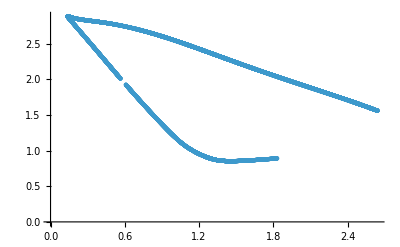

```mathematica
m = 50000;
h = 1/1000;

tlroot["pe"];
c = BUT⟦1, 1, 1;;4⟧;
manp = tlcurve["+h", tlc, c, h, m];

c = BUT⟦-1, 1, 1;;4⟧;
mann = tlcurve["-h", tlc, c, -h, m];

BUS = Join[manp, mann];

midIndex=Floor[Length[BUT]*3/4];

cMid=BUT[[midIndex,1,1;;4]];

manpMid=tlcurve["+h",tlc,cMid,h,m];
mannMid=tlcurve["-h",tlc,cMid,-h,m];

BUSMid=Join[manpMid,mannMid];
combinedManifold=Union[BUS,BUSMid];

ListPlot[combinedManifold[[All,1,{1,2}]],PlotStyle->PointSize[Tiny]]
Save["StateBUone.m", combinedManifold];
```

The evaluation of these two cells results in the gait family data used to simulate impacts in BranchImpacts.nb.